# CSYS5040 Sem2/2020 Assignment 2 SID: 500386873

## Question 1 The dynamics of stochastic differential equation (SDE)

## a. Linear SDE, dx[t] = μ dt +ϵ dw[t]

## i) Effects of μ, and x0

ItoProcess[{{μ},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

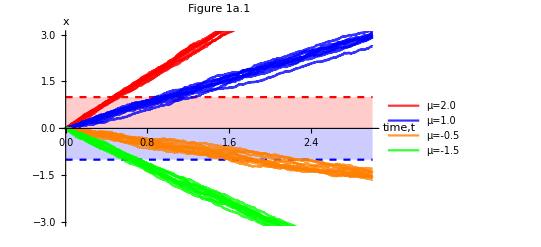

```mathematica
𝒫=ItoProcess[ⅆx[t]== μⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
m = 0.1; (* value of ϵ *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)
b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-3,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-3,3}},Filling->Axis];
p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> 1.0,ϵ->m},{0,3,0.001},10],PlotStyle->{Blue},PlotLegends->{"μ=1.0"},BaseStyle->Directive[Opacity[0.8]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> 2.0,ϵ->m},{0,3,0.001},10],PlotStyle->{Red},PlotLegends->{"μ=2.0"},BaseStyle->Directive[Opacity[0.8]]];
p3= ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> -.5,ϵ->m},{0,3,0.001},10],PlotStyle->{Orange},PlotLegends->{"μ=-0.5"},BaseStyle->Directive[Opacity[0.8]]];
p4 =ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> -1.5,ϵ->m},{0,3,0.001},10],PlotStyle->{Green},PlotLegends->{"μ=-1.5"},BaseStyle->Directive[Opacity[0.8]]];
Show[b1,b2,p2,p1,p3,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.1",LabelStyle->{GrayLevel[0],Bold}]
```

From Figure 1a.1, it is obvious that μ is the gradient of the linear SDE. 
Given unbiased initiate point x0 = 0 and fixed noise term ϵ at 0.1:
When μ is positive,  the solution will never pass the negative boundary, 𝒷2 = -0.1. The greater the +μ, the shorter the time it needs to cross 𝒷1.
Similarly, when the gradient μ is negative, the solution will never cross positive boundary 𝒷1. The greater the -μ, the shorter the time it needs to cross 𝒷2.

ItoProcess[{{μ},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

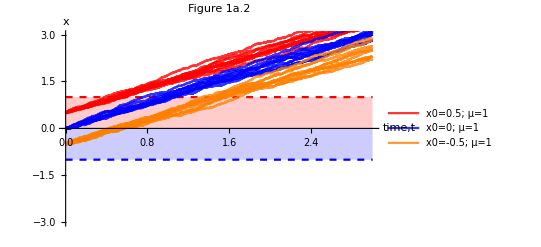

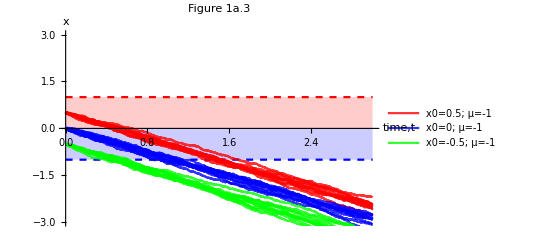

```mathematica
𝒫=ItoProcess[ⅆx[t]== μⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
l = 1; (* value of μ *)
m = 0.1; (* value of ϵ *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)
b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-3,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-3,3}},Filling->Axis];
p1 = ListLinePlot[RandomFunction[𝒫 /.{x0-> 0, μ-> l,ϵ->m},{0,3,0.001},10],PlotStyle->{Blue},PlotLegends->{"x0=0; μ=1"},BaseStyle->Directive[Opacity[0.8]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->0.5, μ-> l,ϵ->m},{0,3,0.001},10],PlotStyle->{Red},PlotLegends->{"x0=0.5; μ=1"},BaseStyle->Directive[Opacity[0.8]]];
p3= ListLinePlot[RandomFunction[𝒫 /.{x0->-0.5, μ-> l,ϵ->m},{0,3,0.001},10],PlotStyle->{Orange},PlotLegends->{"x0=-0.5; μ=1"},BaseStyle->Directive[Opacity[0.8]]];
p4 =ListLinePlot[RandomFunction[𝒫 /.{x0->0.5, μ-> -l,ϵ->m},{0,3,0.001},10],PlotStyle->{Red},PlotLegends->{"x0=0.5; μ=-1"},BaseStyle->Directive[Opacity[0.8]]];
p5 =ListLinePlot[RandomFunction[𝒫 /.{x0->0, μ-> -l,ϵ->m},{0,3,0.001},10],PlotStyle->{Blue},PlotLegends->{"x0=0; μ=-1"},BaseStyle->Directive[Opacity[0.8]]];
p6 =ListLinePlot[RandomFunction[𝒫 /.{x0->-0.5, μ-> -l,ϵ->m},{0,3,0.001},10],PlotStyle->{Green},PlotLegends->{"x0=-0.5; μ=-1"},BaseStyle->Directive[Opacity[0.8]]];
G1=Show[b1,b2,p2,p1,p3,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.2",LabelStyle->{GrayLevel[0],Bold}]
G2 =Show[b1,b2,p4,p5,p6,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.3",LabelStyle->{GrayLevel[0],Bold}]
```

For positive gradient (see Figure 1a.2):
Given a biased initial value 0 < x0 < 𝒷1, we observed that the solution crosses the positive boundary earlier than when x0 = 0, given other parameters are set constant.
On the other hand, when x0 is biased at value less than 0, the time needed to cross expected boundary (𝒷1) is longer.
Similarly, for negative gradient (see Figure 1a.3):
Given a biased initial value 𝒷2 < x0 < 0, we observed that the solution crosses the negative boundary earlier than when x0 = 0, given other parameters are set constant.
On the other hand, when x0 is biased at > 0, the time needed to cross expected boundary (𝒷2) is longer.

## ii) Effect of ϵ, and x0

The variance of SDE is ϵ^2t, and the function ϵ^2(t,x) is the rate at which the variance of the stochastic process grows in time, which is often called diffusion of SDE. 
Noise term ϵ contributes not only to diffusion but also drift of SDE.

```mathematica
𝒫=ItoProcess[ⅆx[t]== μⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
l = 0.7; (* value of μ *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)
b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-3,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-3,3}},Filling->Axis];
p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> l,ϵ->0},{0,3,0.001},20],PlotLegends->"ϵ=0",BaseStyle->Directive[Opacity[0.5]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ->l,ϵ->0.1},{0,3,0.001},20],PlotLegends->"ϵ=0.1",BaseStyle->Directive[Opacity[0.5]]];
p3= ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> l,ϵ->0.5},{0,3,0.001},20],PlotLegends->"ϵ=0.5",BaseStyle->Directive[Opacity[0.5]]];
p4 =ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ->l,ϵ->1.0},{0,3,0.001},20],PlotLegends->"ϵ=1.0",BaseStyle->Directive[Opacity[0.5]]];
G1 =Show[b1,b2,p1,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.4",LabelStyle->{GrayLevel[0],Bold}, ImageSize-> 400];
G2 =Show[b1,b2,p2,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.5",LabelStyle->{GrayLevel[0],Bold}, ImageSize->400];
G3 =Show[b1,b2,p3,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.6",LabelStyle->{GrayLevel[0],Bold}, ImageSize->400];
G4 =Show[b1,b2,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.7",LabelStyle->{GrayLevel[0],Bold}, ImageSize->400];
GraphicsGrid[{{G1,G2},{G3,G4}},ImageSize->Full]
Mean[𝒫[t]]/.{x0->k, μ->l,ϵ->0.1}
Simplify[StandardDeviation[𝒫[t]]]/.{x0->k, μ->l,ϵ->0.1}
```

ItoProcess[{{μ},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

-Graphics-

0.7 t

0.1 √t

When noise term ϵ = 0, basically it becomes a ordinary differential equation (see Figure 1a.4). All simulations yield exactly the same solution, with initial value x0, growing at a gradient  μ. 
When noise term ϵ ≠ 0, the model diffuses over time at value of ϵ√t.
The larger the white noise ϵ , the “noisier” the solution (see Figure 1a.5-7). 
When a touch of noise is added (see Figure 1a.5), the first passage time of all simulations are similar. Increasing ϵ makes them less and less likely to cross the boundary at the same time (see Figure 1a.6).
In fact, the solution is more likely to cross the wrong boundary (𝒷2) when a very large ϵ is introduced, as shown in Figure 1a.7.

```mathematica
𝒫=ItoProcess[ⅆx[t]== μⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
l = 0.7; (* value of μ *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)
b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-3,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-3,3}},Filling->Axis];
p1= ListLinePlot[RandomFunction[𝒫 /.{x0->0, μ-> l,ϵ->1},{0,3,0.001},20],PlotLegends->"x0=0; ϵ=1.0",BaseStyle->Directive[Opacity[0.5]]];
p2 =ListLinePlot[RandomFunction[𝒫 /.{x0->0.5, μ->l,ϵ->1},{0,3,0.001},20],PlotLegends->"x0=0.5; ϵ=1.0",BaseStyle->Directive[Opacity[0.5]]];
G1 =Show[b1,b2,p1,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.7",LabelStyle->{GrayLevel[0],Bold}, ImageSize-> 400];
G2 =Show[b1,b2,p2,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.8",LabelStyle->{GrayLevel[0],Bold}, ImageSize->400];
GraphicsGrid[{{G1,G2}},ImageSize->Full]
```

ItoProcess[{{μ},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

-Graphics-

With a biased prior (x0 = 0.5), the solution is more likely to cross expected boundary even the ϵ is high (compare Figure 1a.7 and 1a.8).

## iii) Passage time of stochastic diffusion towards a boundary value with some confidence intervals

Adding 95% confidence interval limits to the paths: mean ± 2× standard deviation
Here, unbiased x0 is used.

```mathematica
𝒫=ItoProcess[ⅆx[t]== μⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]];
k=0; (* value of x0 *)
l = 0.7; (* value of μ *)
m = 0.1; (* value of ϵ *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)
meanf[t_]=Mean[𝒫[t]]/.{x0->k, μ->l,ϵ->m} (* mean function *)
sdf[t_]=StandardDeviation[𝒫[t]]/.{x0->k, μ->l,ϵ->m}(* standard deviation function *)

b1 =Plot[𝒷1,{t,0,5},PlotStyle->{Dashed, Red},PlotRange->{{0,5},{-1.5,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,5},PlotStyle->{Dashed, Blue},PlotRange->{{0,5},{-1.5,3}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ-> l,ϵ->m},{0,5,0.001},50],BaseStyle->Directive[Opacity[0.5]]];
mean =Plot[meanf[t],{t,0,5},PlotRange-> All,PlotStyle->Directive[Red,Thick, Dashed],PlotLegends->{"mean"}];
uplmt =Plot[meanf[t]+2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Black,Thick, Dashed},PlotLegends->{"upper limit"}];
lowlmt =Plot[meanf[t]-2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Blue,Thick, Dashed},PlotLegends->{"lower limit"}];
Show[{b1,b2,p1,mean,uplmt,lowlmt},AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 1a.9",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
NSolve[meanf[t] == 1,t]
NSolve[meanf[t]+2 *sdf[t] == 1,t]
NSolve[meanf[t]-2 *sdf[t] == 1,t]
```

0.7 t

0.1 √t

-Graphics-

{{t→1.42857}}

{{t→1.12546}}

{{t→1.81331}}

Expectation of the time when the solution cross the boundary is the time when the mean of the solution (red-dashed line) crossing it. Without simulating paths, we could calculate it using equation:
It is known that x = μ t +x0, hence when x or the expected boundary = 1, μ =0.7 and x0 = 0, the expected time, t is (1-0)/0.7 = 1.429 period.
From Figure 1a.9, the 50 simulated paths cross 𝒷1 at a range of time 1.1 to 1.8 period.

## b. Non-linear SDE, dx[t] = -(β x[t]^3 + α x[t] + μ) dt + ϵ dw[t]

## i) Effect of parameters in deterministic part of equation

### Effect of β

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

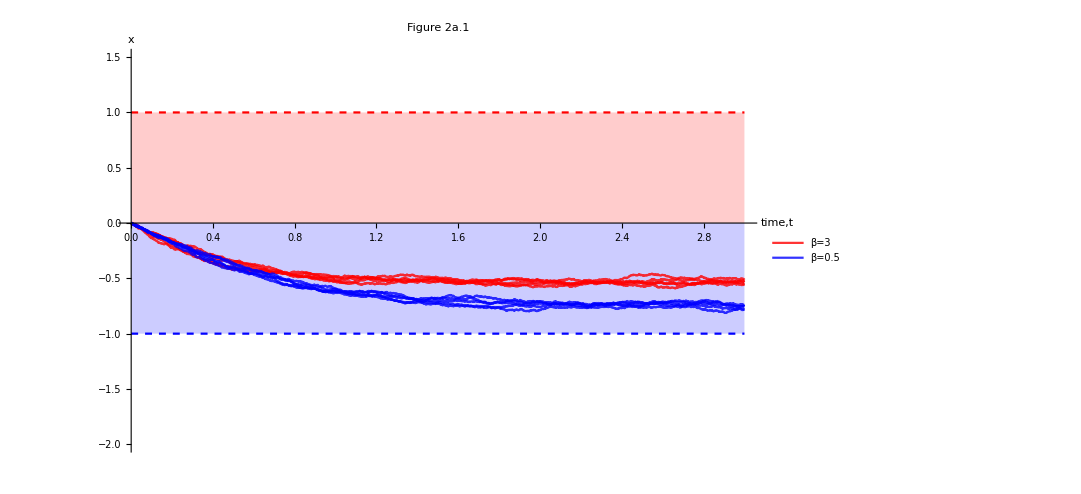

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
l=1; (* value of μ *)
m=0.05; (* value of ϵ *)
r=1; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> 0.5,α -> r,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Blue},PlotLegends->{"β=0.5"},BaseStyle->Directive[Opacity[0.8]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> 3,α -> r,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Red},PlotLegends->{"β=3"},BaseStyle->Directive[Opacity[0.8]]];

Show[b1,b2,p2,p1,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.1",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

With a negative sign in front of the deterministic part, indicating the actual β in this example is negative. From Figure 2a.1, it is seen that the greater the β, the faster the path converges to the equilibrium state.

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

General::ovfl: Overflow occurred in computation.

Experimental`NumericalFunction::nnum: The function value Overflow[] is not a number at {t,x,RandomProcesses`SimulationDump`dt$1502,RandomProcesses`SimulationDump`dw$1502} = {1.896,-1.048944434999619`15.954589770191005*^459677841628934,0.001,1.55069}.

Show::gcomb: Could not combine the graphics objects in ….

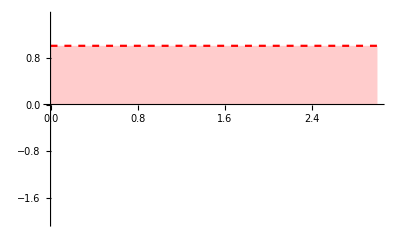
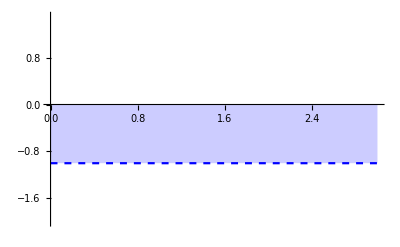
Show[-Graphics-,-Graphics-,p3,AxesLabel→{time,t,x},PlotLabel→Figure 2a.2,LabelStyle→{GrayLevel[0],Bold},ImageSize→800]

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
l=1; (* value of μ *)
m=0.05; (* value of ϵ *)
r=1; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];

p3= ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> -1,α -> r,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Orange},PlotLegends->{"β=-1.0"},BaseStyle->Directive[Opacity[0.8]]];
(*
p4 =ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> -.5,α -> r,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Green},PlotLegends->{"β=-0.5"},BaseStyle->Directive[Opacity[0.8]]];
*)

Show[b1,b2,p3,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.2",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

Unfortunately, the actual positive β applied by giving a negative value to the same model, could not be handled by Mathematica due to overflow issue.

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
Mean[𝒫[t]]/.{x0->0.7, β-> 0.5,α -> 2,μ->3,ϵ->0.05}
Simplify[StandardDeviation[𝒫[t]]]/.{x0->-0.7, β-> 0.5,α -> 2,μ->3,ϵ->0.05}
```

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

Mean[ItoProcess[{{-3-2 x[t]-0.5 x[t]^3},{{0.05}},x[t]},{{x},{0.7}},{t,0}][t]]

StandardDeviation[ItoProcess[{{-3-2 x[t]-0.5 x[t]^3},{{0.05}},x[t]},{{x},{-0.7}},{t,0}][t]]

### Effect of α

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

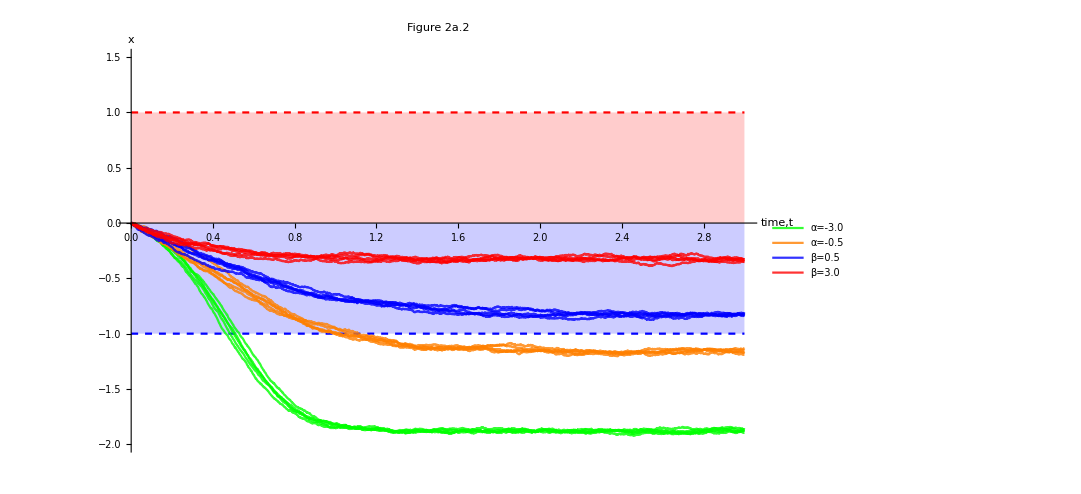

```mathematica
𝒫=ItoProcess[ⅆx[t]==-(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
l=1; (* value of μ *)
m = 0.05; (* value of ϵ *)
q = 1 ;(*value of β*)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];

p1= ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> -0.5 ,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Orange},PlotLegends->{"α=-0.5"},BaseStyle->Directive[Opacity[0.8]]];
p2 =ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> -3,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Green},PlotLegends->{"α=-3.0"},BaseStyle->Directive[Opacity[0.8]]];
p3 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> 0.5,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Blue},PlotLegends->{"β=0.5"},BaseStyle->Directive[Opacity[0.8]]];
p4 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> 3,μ->l,ϵ->m},{0,3,0.001},5],PlotStyle->{Red},PlotLegends->{"β=3.0"},BaseStyle->Directive[Opacity[0.8]]];

Show[b1,b2,p2,p1,p3,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.2",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

From Figure 2a.2, we could see that actual positive α (with negative input as shown by green and orange paths) has greater effect towards the model, than the actual negative values (blue and red paths). This is told by the fact that they cross the expected threshold (𝒷2) while the others do not. It is thus concluded that the higher the value of α, the higher the value of x when t -> ∞.

### Effect of μ

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

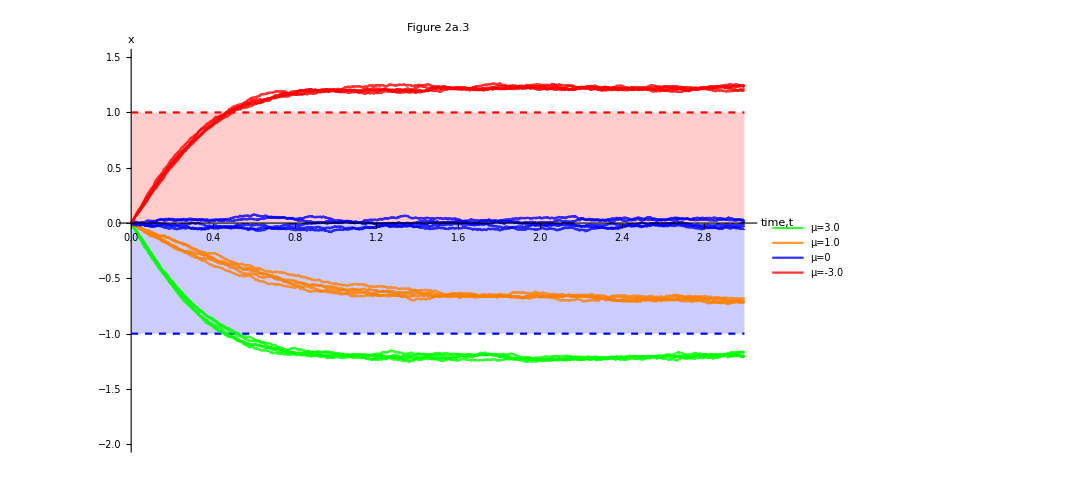

```mathematica
𝒫=ItoProcess[ⅆx[t]==-(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
m=0.05; (* value of ϵ *)
q=1 ;(*value of β*)
r=1; (* value of α *)
𝒷1=1; 𝒷2=-1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,1.5}},Filling->Axis];

p1= ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r ,μ-> 1,ϵ->m},{0,3,0.001},5],PlotStyle->{Orange},PlotLegends->{"μ=1.0"},BaseStyle->Directive[Opacity[0.8]]];
p2 =ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->3,ϵ->m},{0,3,0.001},5],PlotStyle->{Green},PlotLegends->{"μ=3.0"},BaseStyle->Directive[Opacity[0.8]]];
p3 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->0,ϵ->m},{0,3,0.001},5],PlotStyle->{Blue},PlotLegends->{"μ=0"},BaseStyle->Directive[Opacity[0.8]]];
p4 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->-3,ϵ->m},{0,3,0.001},5],PlotStyle->{Red},PlotLegends->{"μ=-3.0"},BaseStyle->Directive[Opacity[0.8]]];

Show[b1,b2,p2,p1,p3,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.3",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

With unbiased x0, when μ = 0, the solutions settle in a stationary state of x = 0 (see Figure 2a.3 blue paths). The higher magnitude of μ gives higher magnitude of equilibrium state the solution converges to, whereby when t -> ∞, the actual positive μ (red paths) yields positive x and actual negative μ (green and orange paths) negative x.

## ii) Effect of ϵ, and x0

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
k=0; (* value of x0 *)
l=0.2; (* value of μ *)
q=1 ;(*value of β*)
r=-3; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,2}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,2}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->0},{0,3,0.001},20],PlotLegends->"ϵ=0",BaseStyle->Directive[Opacity[0.8]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->0.02},{0,3,0.001},20],PlotLegends->"ϵ=0.02",BaseStyle->Directive[Opacity[0.8]]];
p3 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->0.1},{0,3,0.001},20],PlotLegends->"ϵ=0.1",BaseStyle->Directive[Opacity[0.8]]];
p4 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->0.2},{0,3,0.001},20],PlotLegends->"ϵ=0.2",BaseStyle->Directive[Opacity[0.8]]];

G1 =Show[b1,b2,p1,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.4",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G2 =Show[b1,b2,p2,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.5",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G3 =Show[b1,b2,p3,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.6",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G4 =Show[b1,b2,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.7",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];

GraphicsGrid[{{G1,G2},{G3,G4}},ImageSize->Full]
```

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

-Graphics-

When there is no noise term, the all the simulated paths are deterministic and have the same passage time (see Figure 2a.4). 
When a touch of noise is added, the simulations cross the boundary in a small range of period and are attracted to the same stationary state (see Figure 2a.5).
When noise increases, the simulations cross the boundary at deviate times, but eventually settle in and fluctuate around the stationary state when t -> ∞ . Notice that in Figure 2a.6 some paths are attracted to another positive equilibrium state and cross the positive boundary; When we further increase the noise, more paths tend to cross the positive threshold as shown in Figure 2a.7.

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
l=0.2; (* value of μ *)
m=0.1; (* value of ϵ *)
q=1 ;(*value of β*)
r=-3; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

b1 =Plot[𝒷1,{t,0,3},PlotStyle->{Dashed, Red},PlotRange->{{0,3},{-2,2}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,3},PlotStyle->{Dashed, Blue},PlotRange->{{0,3},{-2,2}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->0.05, β-> q,α -> r,μ->l,ϵ->m},{0,3,0.001},50],PlotLegends->"x0=0.05; ϵ=0.1",BaseStyle->Directive[Opacity[0.5]]];
p2 = ListLinePlot[RandomFunction[𝒫 /.{x0->0.1, β-> q,α -> r,μ->l,ϵ->m},{0,3,0.001},50],PlotLegends->"x0=0.1; ϵ=0.1",BaseStyle->Directive[Opacity[0.5]]];
p3 = ListLinePlot[RandomFunction[𝒫 /.{x0->-0.05, β-> q,α -> r,μ->l,ϵ->m},{0,3,0.001},50],PlotLegends->"x0=-0.05; ϵ=0.1",BaseStyle->Directive[Opacity[0.5]]];
p4 = ListLinePlot[RandomFunction[𝒫 /.{x0->-0.1, β-> q,α -> r,μ->l,ϵ->m},{0,3,0.001},50],PlotLegends->"x0=-0.1; ϵ=0.1",BaseStyle->Directive[Opacity[0.5]]];

G1 =Show[b1,b2,p1,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.8",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G2 =Show[b1,b2,p2,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.9",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G3 =Show[b1,b2,p3,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.10",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];
G4 =Show[b1,b2,p4,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.11",LabelStyle->{GrayLevel[0],Bold},ImageSize->400];

GraphicsGrid[{{G1,G2},{G3,G4}},ImageSize->Full]
```

ItoProcess[{{-μ-α x[t]-β x[t]^3},{{ϵ}},x[t]},{{x},{x0}},{t,0}]

-Graphics-

With the same amount of noise used in Figure 2a.6, where ϵ =0.1, we now repeat the process with priors that are a little biased (both positive and negative).
When a positive biased x0 is applied, we notice that more paths are attracted to positive stationary state (see Figures 2a.8-9).
While when a slightly negative biased x0 is used, we observe paths are less likely to cross the positive threshold (see Figures 2a.10-11).

## iii) Passage time of stochastic diffusion towards a boundary value

### dx[t] = -(β x[t]^3 + α x[t] + μ) dt + ϵ dw[t]

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]];
k=0; (* value of x0 *)
l=0.05; (* value of μ *)
m=0.05; (* value of ϵ *)
q=1 ;(*value of β*)
r=-2; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

meanf[t_]=Mean[𝒫[t]]/.{x0->k, β-> q,α -> r,μ->l,ϵ->m} (* mean function *)
sdf[t_]=StandardDeviation[𝒫[t]]/.{x0->k, β-> q,α -> r,μ->l,ϵ->m}(* standard deviation function *)

b1 =Plot[𝒷1,{t,0,5},PlotStyle->{Dashed, Red},PlotRange->{{0,5},{-1.5,2}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,5},PlotStyle->{Dashed, Blue},PlotRange->{{0,5},{-1.5,2}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->m},{0,5,0.001},50],BaseStyle->Directive[Opacity[0.5]]];
(*
mean =Plot[meanf[t],{t,0,5},PlotRange-> All,PlotStyle->Directive[Red,Thick, Dashed],PlotLegends->{"mean"}];
uplmt =Plot[meanf[t]+2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Black,Thick, Dashed},PlotLegends->{"upper limit"}];
lowlmt =Plot[meanf[t]-2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Blue,Thick, Dashed},PlotLegends->{"lower limit"}];
*)
Show[{b1,b2,p1},AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.12",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

Mean[ItoProcess[{{-0.05+2 x[t]-x[t]^3},{{0.05}},x[t]},{{x},{0}},{t,0}][t]]

StandardDeviation[ItoProcess[{{-0.05+2 x[t]-x[t]^3},{{0.05}},x[t]},{{x},{0}},{t,0}][t]]

-Graphics-

Despite the fact that the time (or range of time) where the solution crosses the boundaries are different for each computation, it is observed that the model in general tends to cross negative boundary more than the positive one, the stationary state or the attractor is said to be around -1.4 (see Figure 2a.12).

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]];
k=-1.4; (* value of x0 *)
l=0.05; (* value of μ *)
m=0.05; (* value of ϵ *)
q=1 ;(*value of β*)
r=-2; (* value of α *)
𝒷1 = 1; 𝒷2 = -1; (* value of boundaries *)

meanf[t_]=Mean[𝒫[t]]/.{x0->k, β-> q,α -> r,μ->l,ϵ->m} (* mean function *)
sdf[t_]=StandardDeviation[𝒫[t]]/.{x0->k, β-> q,α -> r,μ->l,ϵ->m}(* standard deviation function *)

b1 =Plot[𝒷1,{t,0,5},PlotStyle->{Dashed, Red},PlotRange->{{0,5},{-1.5,2}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,5},PlotStyle->{Dashed, Blue},PlotRange->{{0,5},{-1.5,2}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, β-> q,α -> r,μ->l,ϵ->m},{0,5,0.001},50],BaseStyle->Directive[Opacity[0.5]]];
(*
mean =Plot[meanf[t],{t,0,5},PlotRange-> All,PlotStyle->Directive[Red,Thick, Dashed],PlotLegends->{"mean"}];
uplmt =Plot[meanf[t]+2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Black,Thick, Dashed},PlotLegends->{"upper limit"}];
lowlmt =Plot[meanf[t]-2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Blue,Thick, Dashed},PlotLegends->{"lower limit"}];
*)
Show[{b1,b2,p1},AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.13",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

Mean[ItoProcess[{{-0.05+2 x[t]-x[t]^3},{{0.05}},x[t]},{{x},{-1.4}},{t,0}][t]]

StandardDeviation[ItoProcess[{{-0.05+2 x[t]-x[t]^3},{{0.05}},x[t]},{{x},{-1.4}},{t,0}][t]]

-Graphics-

Figure 2a.13 shows the case where initial condition x0 equals to long term mean.

### Ornstein-Uhlenbeck model (with 95% confidence interval applied)

```mathematica
𝒫=ItoProcess[ⅆx[t]== γ(μ-x[t])ⅆt+σⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[0,1]]
k=0; (* value of x0 *)
l=1.5; (* value of μ *)
m=4; (* value of γ *)
n=0.5;(*value of σ*)
𝒷1 = 1;𝒷2 = -1; (*value of boundaries*)

meanf[t_]=Mean[𝒫[t]]/.{x0->k, μ->l,γ-> m, σ->n} (* mean function *)
sdf[t_]=StandardDeviation[𝒫[t]]/.{x0->k, μ->l,γ-> m, σ->n}(* standard deviation function *)
Limit[Mean[𝒫[t]],t-> ∞]
Limit[StandardDeviation[𝒫[t]],t-> ∞]

b1 =Plot[𝒷1,{t,0,5},PlotStyle->{Dashed, Red},PlotRange->{{0,5},{-1.5,3}},Filling->Axis];
b2 =Plot[𝒷2,{t,0,5},PlotStyle->{Dashed, Blue},PlotRange->{{0,5},{-1.5,3}},Filling->Axis];

p1 = ListLinePlot[RandomFunction[𝒫 /.{x0->k, μ->l,γ-> m, σ->n},{0,5,0.001},20],BaseStyle->Directive[Opacity[0.5]]];
mean =Plot[meanf[t],{t,0,5},PlotRange-> All,PlotStyle->Directive[Red,Thick, Dashed],PlotLegends->{"mean"}];
uplmt =Plot[meanf[t]+2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Black,Thick, Dashed},PlotLegends->{"upper limit"}];
lowlmt =Plot[meanf[t]-2 *sdf[t],{t,0,5},PlotRange-> All,PlotStyle->{Blue,Thick, Dashed},PlotLegends->{"lower limit"}];

Show[{b1,b2,p1,mean,uplmt,lowlmt},AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 2a.14",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]

NSolve[meanf[t] == 1,t]
NSolve[meanf[t]+2 *sdf[t] == 1,t]
NSolve[meanf[t]-2 *sdf[t] == 1,t]
```

ItoProcess[{{γ μ-γ x[t]},{{σ}},x[t]},{{x},{x0}},{t,0}]

1.5 ⅇ^(-4 t) (-1+ⅇ^(4 t))

0.176777 √(ⅇ^(-8 t) (-1+ⅇ^(8 t)))

ConditionalExpression[μ, (x0|μ)∈ℝ&&γ>0]

ConditionalExpression[(√(σ^2/γ))/(√2), σ^2∈ℝ&&γ>0&&σ≠0]

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.274653}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.157405},{t→0.157405-1.5708 ⅈ},{t→0.157405+1.5708 ⅈ},{t→0.157405+3.14159 ⅈ}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.578705},{t→0.578705-1.5708 ⅈ},{t→0.578705+1.5708 ⅈ},{t→0.578705+3.14159 ⅈ}}

From this plot of O-U model we observe that the passage time of the paths is between 0.15 to 0.6 period and with an expectation of x = 1.5 at 0.27 period.

## c. Application of the methods

## Combining Choices and Response Times in the Field: A Drift-Diffusion Model of Mobile Advertisements

Chiong, Khai and Shum, Matthew and Webb, Ryan and Chen, Richard, Combining Choices and Response Times in the Field: A Drift-Diffusion Model of Mobile Advertisements (January 14, 2019). Available at SSRN: https://ssrn.com/abstract=3289386 or http://dx.doi.org/10.2139/ssrn.3289386
"https://economics.princeton.edu/wp-content/uploads/2019/08/Combining-Choices-and-Response.pdf"

In this article, Chiong et al. analyse the users’ choices and their response times to video advertisements on mobile devices. The authors adapt a two-stage drift-diffusion model (DDM) to assess the optimal design and format of advertisements by investigating the behaviour of users in ad exposure stage and decision stage. In the first stage users were “forced” to watch the entire 30 seconds video ad and were then asked to make a decision in the second stage. The choices available were to either click-through to download the advertised app (positive threshold) or to click-back to return to the original app (negative threshold). From the result of the first stage, the authors found that there are two types of user (by which are then referred to as “positive users” and “negative users”), based on their estimated diffusion process drift towards or away the positive threshold. In this paper, the negative users are found to have a lower click-through rate and a shorter response time than the positive users. Behaviour of users towards non-skippable and skippable ads were also studied. Interestingly, the authors found out that the revenue for allowing viewers to skip the ad after 3 seconds are similar to that forcing them to watch the full 30 seconds-ad. In fact, as negative users are more appealed by short ads, publishers can optimise and increase their revenue by customizing their ads according to users’ demographics. The authors conclude by highlighting three extensions of the study, including the extension of DDM for multinomial choices, in which the first of N accumulation processes that hits a threshold is chosen.

## Question 2 Plotting non-linear functions for a non-linear map

## a. Return map of x(t+1) vs. x(t)

## Logistic map

x0 = 0.1 and r = 4

```mathematica
α= 4;
logistic=Drop[N@RecurrenceTable[{x[t+1]==α x[t](1-x[t]),x[0]==0.1},x[t],{t,4501}],501];
Show[ListPlot[Partition[logistic,2,1], GridLines->Automatic],PlotLabel->"Figure 2a",AxesLabel->{HoldForm[x [t]],HoldForm[x [t+1]]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

-Graphics-

## b. Time series for Logistic map with different parameters

## Chaotic parameter

Logistic map is chaos when r = 4

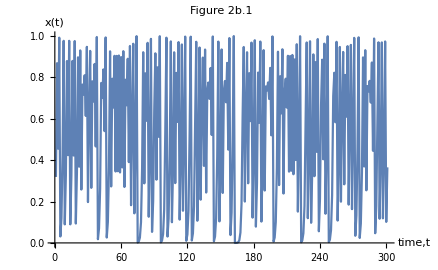

```mathematica
α= 4;
logistic=Drop[N@RecurrenceTable[{x[t+1]==α x[t](1-x[t]),x[0]==0.1},x[t],{t,501}],201];
ListPlot[logistic, Joined->True,PlotLabel->"Figure 2b.1",AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

## Non-chaotic parameter

### an example when r = 3.44949

```mathematica
α= 3.44949;
logistic=Drop[N@RecurrenceTable[{x[t+1]==α x[t](1-x[t]),x[0]==0.1},x[t],{t,501}],201];
ListPlot[logistic, Joined->True,PlotLabel->"Figure 2b.2",AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold},ImageSize->Large]
```

-Graphics-

### time series when varying parameter r

```mathematica
Manipulate[
timelen = 300;
ListLinePlot[
     (* If[ drugi,
     {NestList[a # (1-#)&,x0,timelen],
     NestList[a # (1-#)&,If[x0+roz<0,0,If[x0+roz>1,1,x0+roz],x0+roz],timelen]},*)
       NestList[a # (1-#)&,x0,timelen] ,
      PlotRange->{{0,timelen},{0,1}},
      PlotStyle->{Directive[RGBColor[.6,.73,.36], Thick] (*,If[drugi,RGBColor[1,.47,0], RGBColor[.6,.73,.36]]*)},
     DataRange->{0,timelen},
PlotLabel->"Time Series of the Logistic Map"  ,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold},ImageSize->Large],
{{a,3.45,"a"},0,4,0.0001,Appearance->"Labeled"},
{{x0,0.1,"Seed x_0"},0,1,Appearance->"Labeled"},
(*{{drugi, True, "Second solution?"}, {True, False}},
{{roz, 0.00001, "Difference δ between initial values"}, -x0, x0, 0.00001, Appearance->"Labeled"},*)
TrackedSymbols:>Manipulate
]
```

When r is between 0 and 1, long term x is zero despite of any value of initial condition x0.
When r is between 1 and 2, long term x is observed to be 0.5, again, independent of initial value x0.
When r is between 2 and 3, x fluctuate in the beginning but eventually approach a constant, where increasing r increases long term x (0.5 to 0.65).
When r is between 3 and around 3.44949 (which is 1 + 6^(1/2)), x will oscillate between two values (which depend on r) in long term.
When r is between 3.44949 and 3.54409, x is observed to oscillate between four values in long term.
When r is beyond 3.54409, x oscillates between more values (8, 16 etc) in long term.
When r is beyond 3.56995, most r exhibits chaotic behavior excepts for some islands of stability.
Pomeau–Manneville scenario: chaotic behavior when r lies between 3.56995 and 3.82843

**Ranges of r and their behavior are taken from Wikipedia ( https://en.wikipedia.org/wiki/Logistic_map#Behavior_dependent_on_r ), and verified by playing with the dynamic plot above.

## c. Bifurcation and Lyapunov plots

## Bifurcation diagrams

```mathematica
LogisticEqn[xmin_,xmax_,ymin_,ymax_]:= Module[{f,μ},
f:=Compile[{{μ,_Real}},({μ,#}&)/@Union[Drop[NestList[μ # (1-#)&,.01,1000],300]]];


ListPlot[
Flatten[Table[f[μ],{μ,xmin,xmax,(xmax-xmin)/2000}],1],
PlotStyle->{Red,AbsolutePointSize[0.5]},Frame->True,
FrameLabel->TraditionalForm/@{r,x},PlotLabel->TraditionalForm[Subscript[x, n]==r Subscript[x, n-1](1-Subscript[x, n-1])],
GridLines->Automatic,LabelStyle->{12,GrayLevel[0],Bold},PlotRange->{{xmin, xmax},{ymin,ymax}},
ImageSize->Large
]
]
```

```mathematica
LogisticEqn[0.5,4,0,1]
```

-Graphics-

```mathematica
LogisticEqn[3.5,4,0,1]
```

-Graphics-

```mathematica
LogisticEqn[3.5,3.8,0.8,0.95]
```

-Graphics-

```mathematica
LogisticEqn[3.5,3.6,0.35,0.4]
```

-Graphics-

```mathematica
LogisticEqn[3.56,3.58,0.36,0.39]
```

-Graphics-

```mathematica
LogisticEqn[3.568,3.57,0.378,0.382]
```

-Graphics-

Fractal is identified: Magnification of bifurcation diagram of Logistic Map depicts that it exhibits self-similarity, where self-similar patterns repeat at different scales.

## Lyapunov exponent diagram

```mathematica
Lyapunov[X0_,a_,N_]:=Module[{f,F,X,exp}, 
f[x_]:=a x(1-x);
F[x_]:=a(1-2x);
X[n_]:=Nest[f,X0,n];
exp:=Sum[Log[Abs[F[X[n]]]],{n,0,N-1}]/N; 
exp]

Plot[Lyapunov[0.1,a,200],{a,.5,4},PlotStyle->{Blue},PlotRange->{-3.2,1},PlotLabel->"Figure 2c.2",
    AxesLabel->{"r","λ"}, GridLines->Automatic,LabelStyle->{12,GrayLevel[0],Bold},ImageSize->Large]
```

-Graphics-

From Figure 2c.2, it is observed that for r from 0 to approximate 3.55, the largest Lyapunov exponent are all less than zero, and beyond that range, most r values have positive  Lyapunov exponent.

## Question 3 Parameters in non-linear dynamical systems

## a. Question 1b extension

## Dynamic plot for parameters

Here we are varying only one parameter, which is μ, and observe when does the system change from one stationary state to another.

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]];
Manipulate[
ListLinePlot[RandomFunction[𝒫 /.{x0->s, β-> g,α ->u ,μ-> v,ϵ->w},{0,5,0.001},1],PlotRange->{{0,5},{-2,2}},BaseStyle->Directive[Opacity[0.8]],AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 3a.1",LabelStyle->{GrayLevel[0],Bold},ImageSize-> Large],
{{s,0,"x0"},-2,2,0.001,Appearance->"Labeled"},
{{g,1," β"},1,5,0.001,Appearance->"Labeled"},
{{ u,-2,"α"},-10,10,0.001,Appearance->"Labeled"},
{{ v,0.05,"μ"},-0.2,0.2,0.001,Appearance->"Labeled"},
{{ w,0.05,"ϵ"},0,1,0.001,Appearance->"Labeled"},
TrackedSymbols:>Manipulate
]
```

From Dynamic plot above, by playing the animation for parameter μ, it is observed that the stationary state of the SDE changed from positive to negative when μ ≈ 0 when x0 = 0.

## Tipping point of the system when parameter changes

```mathematica
𝒫=ItoProcess[ⅆx[t]== -(β* x[t]^3+α * x[t]+μ)ⅆt+ϵ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]];
s=0; (* value of x0 *)
v=1 ;(*value of β*)
u=-2; (* value of α *)
w=0.05; (* value of ϵ *)

miu= -0.00173; (*intial value of parameter to vary*)
μMax = 1.35;(*final value of parameter to vary*)
i = 0.001; (*Increment of parameter*)
xlst ={}; (*list to store all x values*)
tlst={}; (*list to store all time*)
idx = 0; (*Increment for time*)
While[miu≤μMax,
td=RandomFunction[𝒫 /.{x0->s, β->v,α ->u ,μ-> miu,ϵ->w},{0,4,0.01}];
If[miu == μMax,
xvalue=td["Values"];
time =td["PathTimes"]+4*idx,
xvalue = Drop[td["Values"],-1];
time= Drop[td["PathTimes"]+4*idx,-1]
];
xlst =Join[xlst,xvalue];
tlst = Join[tlst,time];
s = Last[td["Values"]];
idx += 1;
miu +=i
];
ts =TimeSeries[xlst, {tlst}];
ListLinePlot[ts,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 3a.2",LabelStyle->{GrayLevel[0],Bold},ImageSize-> Large]
```

-Graphics-

```mathematica
nts =TimeSeries[ Drop[xlst,320000],{Drop[tlst,320000]}]
ListLinePlot[nts,AxesLabel->{RawBoxes[RowBox[{"time",",","t"}]],HoldForm[x]},PlotLabel->"Figure 3a.3",LabelStyle->{GrayLevel[0],Bold},ImageSize-> Large]
```

TemporalData[TimeSeries, <<1>>]

-Graphics-

Figure 3a.2 shows the full process of how the system changes from one state to another when μ increases from -0.00173 to 1.35 with 0.001 increment.  It started with x = 0, and all values of x for each increment of  μ, where each iteration consists of 401 data points (since time is taken from 0 to 4 in 0.01 step), and last value of x from each iteration is used as the starting point of x in next iteration. By this, a continuous time series of changing of x is obtained.
Figure 3a.3 gives a closer look into the part of the tipping in time series after the first 3 200 period. Tipping point is seen when t is at approximately 4280 period.

## b. Question 2 extension

## Estimating Lyapunov Exponent from Time Series

### Direct method

The separation of neighbouring states by the distance, d_L(m(n),n, k) = | x(m(n) + (D - 1)L + k) - x(n + (D - 1)L + k)|
where x(m(n)) is the nearest neighbour of reference point x(n),
k is the time steps (denoted by δ in the function below),
D is the difference of the last components of both reconstructed states or reconstruction dimension (denoted by m in the function below), and
L is the time lag used for delay reconstruction (denoted by τ in the function below).

Averaged logarithmic distance, E_L(k) = (1/N)∑ (1/U) ∑ ln  d_L(m(n),n, k)
where N = number of reconstructed states that possess very close neighbours,
U = number of neighbours of x(n)

E(k) = k∆t λ + E(0)
By plotting E(k) vs k∆t where ∆t = 1, we can then obtain the Lyapunov Exponent from the gradient of the linear segment of the graph.

```mathematica
S[data_, τ_, mMax_, ϵ_, δMax_, h_] := {ϵ, h,
  ParallelTable[Module[{emb, nn, nf, neigh},
    emb = Table[Take[data, {i, i + τ (m - 1), τ}], {i, Length[data] - τ (m - 1)}];
    nn = Length[emb];
    nf = Nearest[emb -> Range[nn]];
    neigh = Table[DeleteCases[Rest[nf[emb[[t]], {∞, ϵ}]], p_ /; p > nn - δMax], {t, nn - δMax}];
    Table[{δ, Mean[DeleteCases[Table[If[Length[neigh[[t]]] == 0, "d",Log[Mean[Abs[data[[t + (m - 1) τ + δ]] - data[[neigh[[t]] + (m - 1) τ + δ]]]]]],{t, nn - δMax}], "d"|Indeterminate]]},{δ, 0, δMax}]],
  {m, mMax}]}
```

{{{0,-9.37904},{1,-8.5881},{2,-7.86589},{3,-7.16439},{4,-6.47732},{5,-5.78954},{6,-5.088},{7,-4.40309},{8,-3.71052},{9,-3.02364},{10,-2.3652},{11,-1.78827},{12,-1.31767},{13,-1.07788},{14,-1.1476}},{{0,-9.68042},{1,-8.84207},{2,-8.09121},{3,-7.37074},{4,-6.656},{5,-5.97342},{6,-5.29457},{7,-4.62931},{8,-3.94463},{9,-3.25838},{10,-2.5858},{11,-1.98721},{12,-1.42437},{13,-1.13727},{14,-1.21766}},{{0,-9.80806},{1,-8.93065},{2,-8.14501},{3,-7.37188},{4,-6.66517},{5,-6.00597},{6,-5.35185},{7,-4.686},{8,-3.98116},{9,-3.30634},{10,-2.63569},{11,-2.01313},{12,-1.44612},{13,-1.13833},{14,-1.29291}}}

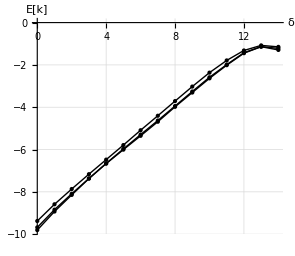

```mathematica
α = 4;
logistic=Drop[N@RecurrenceTable[{x[t+1]==α x[t](1-x[t]),x[0]==0.1},x[t],{t,4501}],501];

Logistic = S[logistic, 1, 3, 0.0002, 14, 1];
{ϵ,h,s}=Logistic;
Table[s⟦m⟧,{m,Length[s]}]
ListLinePlot[Table[s⟦m⟧,{m,Length[s]}],Mesh->All,MeshStyle->AbsolutePointSize[3],PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"δ","E[k]"},PlotStyle->{{Black,AbsoluteThickness[1]}},ImageSize->295,AspectRatio->0.87,GridLines->Automatic]
```

```mathematica
s[[1,1,2]]
```

-9.37904

```mathematica
Slope[table_, m_,pt1_,pt2_]:=Module[{x1,x2,y1,y2,slope},
x1:=table[[m,pt1,1]];
x2:=table[[m,pt2,1]];
y1:=table[[m,pt1,2]];
y2:=table[[m,pt2,2]];
slope := (y2-y1)/(x2-x1);
slope]

Slope[s,1,3,11]
Slope[s,2,3,11]
est =Slope[s,3,3,11]
```

0.687586

0.688176

0.688665

Taking m = 3,
Let point 1 when δ = 2 and point 2 when δ =11.
The slope, λ_1 =  0.688665 (estimated value)

### Analytical method

Lyapunov exponent when r = 4, computed by analytical method:

```mathematica
Lyapunov[X0_,a_,N_]:=Module[{f,F,X,exp}, 
f[x_]:=a x(1-x);
F[x_]:=a(1-2x);
X[n_]:=Nest[f,X0,n];
exp:=Sum[Log[Abs[F[X[n]]]],{n,0,N-1}]/N; 
exp]

exact =Lyapunov[0.1,4,200]
```

0.692844

For Logistic map, Lyapunov exponent ,λ_1 = 0.692844 (exact value)

### Comparison

```mathematica
pctDiff = Abs[exact-est]/exact *100
```

0.603264

Percentage difference = [ |exact λ - estimated λ|/ exact λ] ]x100
= 0.60%

The leading Lyapunov exponent obtained from the Direct method differs from exact value by 0.71%.

## Estimating the Fractal dimension of Logistic Map using the Kaplan-Yorke conjecture

Kaplan–Yorke conjecture:
Fractal dimension, d_f = j + ((∑_(i=1))^j λ_i)/(|λ_(j+1)|) , where j is defined by the condition that (∑_(i=1))^jλ_i > 0, and (∑_(i=1))^(j+1)λ_i < 0

```mathematica
frac = 1 + exact
```

1.69284

Hence, d_f = j + λ_1 = 1.69284